```mathematica
从P倒推需要的Mdot
假设现在源处于spin equilibrium，又现在的周期P推出此时的Mdot，并由此倒推初始盘的质量和回落盘形成时间;
P1=1.427579,Pdot1=-9.6*^-9;MJD1=52690.9;
P2=1.137403,Pdot2=-5.2*^-9;MJD2=56848.0;
P3=1.137316,Pdot3=-5.0*^-9;MJD3=56848.2;
P4=1.136042,Pdot4=-4.7*^-9;MJD4=56851.5;
MJD in units of day;
```

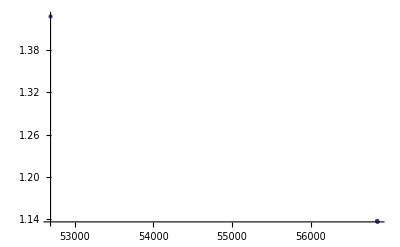

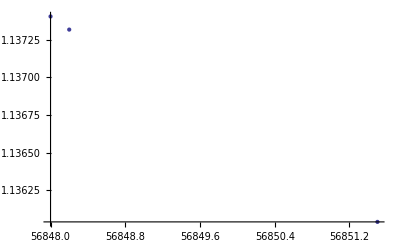

```mathematica
data={{52690.9,1.427579},{56848.0,1.137403},{56848.2,1.137316},{56851.5,1.136042}};
ListPlot[data]
ListPlot[data[[2;;4]]]
```

```mathematica
拉格朗日插值多项式,4点
```

```mathematica
Clear["`*"]

P1=1.427579;MJD1=52690.9;
P2=1.137403;MJD2=56848.0;
P3=1.137316;MJD3=56848.2;
P4=1.136042;MJD4=56851.5;

y0=P1;x0=MJD1;
y1=P2;x1=MJD2;
y2=P3;x2=MJD3;
y3=P4;x3=MJD4;

p3x=y0*((x-x1)*(x-x2)*(x-x3))/((x0-x1)*(x0-x2)*(x0-x3))+y1*((x-x0)*(x-x2)*(x-x3))/((x1-x0)*(x1-x2)*(x1-x3))+y2*((x-x0)*(x-x1)*(x-x3))/((x2-x0)*(x2-x1)*(x2-x3))+y3*((x-x0)*(x-x1)*(x-x2))/((x3-x0)*(x3-x1)*(x3-x2))
```

-1.98537×10^-11 (-56851.5+x) (-56848.2+x) (-56848.+x)+0.000390864 (-56851.5+x) (-56848.2+x) (-52690.9+x)-0.000414501 (-56851.5+x) (-56848.+x) (-52690.9+x)+0.0000236405 (-56848.2+x) (-56848.+x) (-52690.9+x)

```mathematica
拉格朗日插值多项式,3点
```

```mathematica
Clear["`*"]

P1=1.427579;MJD1=52690.9;
P2=1.137403;MJD2=56848.0;
P3=1.137316;MJD3=56848.2;
P4=1.136042;MJD4=56851.5;

y0=P2;x0=MJD2;
y1=P3;x1=MJD3;
y2=P4;x2=MJD4;

p2x=y0*((x-x1)*(x-x2))/((x0-x1)*(x0-x2))+y1*((x-x0)*(x-x2))/((x1-x0)*(x1-x2))+y2*((x-x0)*(x-x1))/((x2-x0)*(x2-x1))
```

1.62486 (-56851.5+x) (-56848.2+x)-1.72321 (-56851.5+x) (-56848.+x)+0.0983586 (-56848.2+x) (-56848.+x)

```mathematica
x=MJD1;
y=1.6248614285950733 (-56851.5+x) (-56848.2+x)-1.7232060606296167 (-56851.5+x) (-56848.+x)+0.09835861471852797 (-56848.2+x) (-56848.+x)
```

244.599

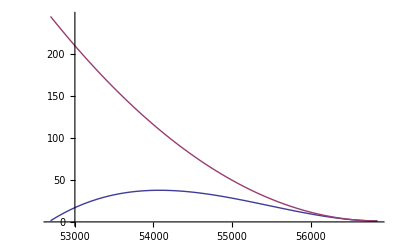

```mathematica
Clear[x]
y1=-1.9853740863505013*^-11 (-56851.5+x) (-56848.2+x) (-56848.+x)+0.0003908641669902273 (-56851.5+x) (-56848.2+x) (-52690.9+x)-0.0004145012533686813 (-56851.5+x) (-56848.+x) (-52690.9+x)+0.00002364048808309571 (-56848.2+x) (-56848.+x) (-52690.9+x);
y2=1.6248614285950733 (-56851.5+x) (-56848.2+x)-1.7232060606296167 (-56851.5+x) (-56848.+x)+0.09835861471852797 (-56848.2+x) (-56848.+x);
Plot[{y1,y2},{x,52690,56852}]
```

```mathematica
Clear["`*"]

P1=1.427579;MJD1=52690.9;
P2=1.137403;MJD2=56848.0;
P3=1.137316;MJD3=56848.2;
P4=1.136042;MJD4=56851.5;

x0=P1;y0=MJD1;
x1=P2;y2=MJD2;
x2=P3;y2=MJD3;
x3=P4;y3=MJD4;

(*p3x=y0*□/□+y1*□/□+y2*□/□+y3*□/□;*)

G=6.67*10^-8;
Msun=2.*10^33;
c=3.*10^10;
R=10^6;
m=1.4;
MdotEdd=1.39*10^18*m;(*Eddington accretion rate*)
M=m*Msun;
Irot=10^45;
xi=0.5;

P1=1.427579;
MJD1=52690.9;

Mdot=5*10^18;

B=10^15;
mu=0.5*B*R^3;
Rin=xi*(mu^4/(2*G*M*Mdot^2))^(1/7);


P=P1;
t=MJD1*24*3600.;
MJD4=56851.5*24*3600.;

dataP=Table[
n;
torque=Mdot*(G*M*Rin)^(1/2);
Pdot=-(torque*P^2.)/(2.*Pi*10^45.);
dt=If[t<MJD4,Min[10^-3*P/Abs[Pdot],10^-3*t],0];
t=t+dt;
P=P+Pdot*dt;
(*t=t/(24*3600.);*)
{t,P},
{n,1,1000}];
```